```mathematica
Clear["Global`*"]
```

```mathematica
(*把HH模型降维到二维*)
```

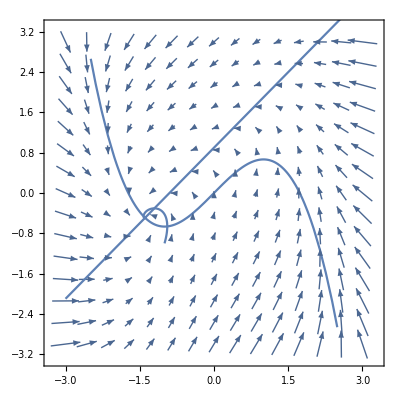

```mathematica
Is=0;
ϵ=1.25;
b0=0.9;
b1=1.0; 
du=u-1/3 u^3-w+Is;
dw=ϵ*(b0+b1*u-w);
linew=b0+b1*u;
lineu=u-(1/3)*u^3;
vp=VectorPlot[{du,dw},{u,-3, 3}, {w, -3, 3}];
up=Plot[lineu,{u,-3,3}];
wp=Plot[linew,{u,-3,3}];
sol=NDSolve[{u'[t]==u[t]-(1/3)*u[t]^3-w[t],w'[t]==ϵ*(b0+b1*u[t]-w[t]),u[0]==-1,w[0]==-1},{u,w},{t,0,100}];
pp=ParametricPlot[{u[t],w[t]}/.First@sol//Evaluate,{t,0,100},PlotRange->All,PerformanceGoal->"Quality"];
Show[{vp,up,wp,pp}]
```